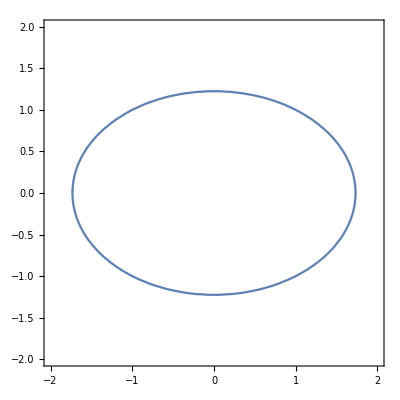

```mathematica
(*Задание 1*)
(*Построить график эллипса X^2+2*Y^2=3, используя ContourPlot[] пакета математки*)
AbsScaleX1=2;
AbsScaleY1=2;
ContourPlot[x^2+2*y^2==3,{x,-AbsScaleX1,AbsScaleX1},{y,-AbsScaleY1,AbsScaleY1}]
```

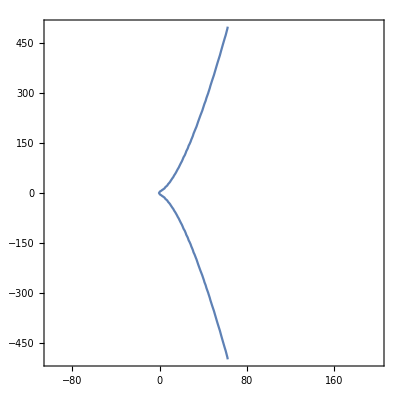

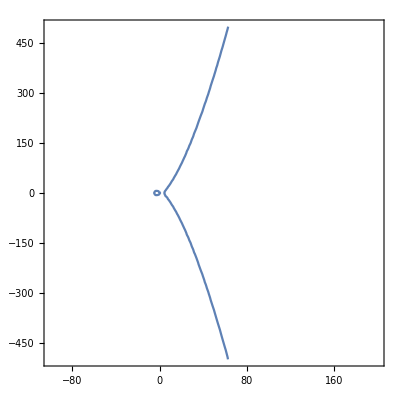

```mathematica
(*Задание 2*)
(*В поле рациональных чисел построить графики эллиптических кривых Y^2=X^3+a*X+b для положительного и отрицательного коэффициента a*)
(*y^2==x^3+22x+11*)
a=22;
b=11;
p=83;
n=5;
AbsScaleX2=100;
AbsScaleY2=500;
ContourPlot[y^2==x^3+a*x+b,{x,-AbsScaleX2,AbsScaleX2+100},{y,-AbsScaleY2,AbsScaleY2}]
ContourPlot[y^2==x^3-a*x+b,{x,-AbsScaleX2,AbsScaleX2+100},{y,-AbsScaleY2,AbsScaleY2}]
```

```mathematica
(*Задание 3*)
(*Проверить выполенение условия гладкости кривой -16(4*a^3+27*b^2)≠0*)
-16*(4*a^3+27*b^2)≠0
```

True

```mathematica
(*Проверить, является ли заданный в правой части уравнения многочлен неприводимым, используя функцию Factor[]*)
Factor[x^3+a*x+b]
```

11+22 x+x^3

```mathematica
(*Проверить выполнение условия гладкости кривой в GF(p)*)
```